P(λ | n,a)

```mathematica
Pλ[n_,a_]:=PDF[GammaDistribution[n+1-a, 1],λ]
```

P(L | λ,a,b)

```mathematica
PL[λ_,a_,b_]:=PDF[NormalDistribution[λ a,√(λ b)],L]
PL[λ,a,b]
```

(ⅇ^(-(L-a λ)^2/(2 b λ)))/(√(2 π) √(b λ))

P(a,b | n, {l_i}) is a Normal-InverseGamma with that conjugate prior

```mathematica
ConjugatePrior[a_,b_,μ0_,n0_,ν0_,ν0σ0Sq_]:=PDF[NormalDistribution[μ0,√((b-a^2)/n0)],a] PDF[InverseGammaDistribution[ν0/2,ν0σ0Sq/2],b-a^2]
P[nSamples_,sampleMean_, sumSquaredDiff_,μ0_,n0_,ν0_,σ0Sq_]:=Module[{μ,n,ν,νσSq},
n=n0+nSamples;
μ=(n0 μ0+nSamples sampleMean)/n;
ν=ν0+nSamples;
νσSq=ν0 σ0Sq + sumSquaredDiff+(n0 nSamples)/n(μ0-sampleMean)^2;
ConjugatePrior[a,b,μ,n,ν,νσSq]
]
P["N", mean, sec, μ0, n0, ν0, σ0Sq]//Simplify
```

Piecewise[{{-(2^(1/2 (-1-N-ν0)) ⅇ^((N (a-mean)^2+a^2 n0+sec-2 a n0 μ0+n0 μ0^2+ν0 σ0Sq)/(2 (a^2-b))) ((sec+(N n0 (mean-μ0)^2)/(N+n0)+ν0 σ0Sq)/(-a^2+b))^((N+ν0)/2))/((a^2-b) √((-a^2+b)/(N+n0)) √π Gamma[(N+ν0)/2]), a^2<b}, {0, True}}]

Put it all together: no analytical integral possible

```mathematica
PL[λ,a,b] Pλ[n,a]P["N", mean, sec, μ0, n0, ν0, σ0Sq]//Simplify
%[[1,1,1]]//Log//Simplify
```

Piecewise[{{-(2^(1/2 (-2-N-ν0)) ⅇ^((2 a^3 L λ-a^4 λ^2+a^2 (-L^2+b (N+n0-λ) λ)-2 a b λ (L+N mean+n0 μ0)+b (L^2+λ (N mean^2+sec+2 b λ+n0 μ0^2+ν0 σ0Sq)))/(2 (a^2-b) b λ)) λ^(-a+n) ((sec+(N n0 (mean-μ0)^2)/(N+n0)+ν0 σ0Sq)/(-a^2+b))^((N+ν0)/2))/((a^2-b) √((-a^2+b)/(N+n0)) π √(b λ) Gamma[1-a+n] Gamma[(N+ν0)/2]), λ>0&&a^2<b}, {0, True}}]

Log[-(2^(1/2 (-2-N-ν0)) ⅇ^((2 a^3 L λ-a^4 λ^2+a^2 (-L^2+b (N+n0-λ) λ)-2 a b λ (L+N mean+n0 μ0)+b (L^2+λ (N mean^2+sec+2 b λ+n0 μ0^2+ν0 σ0Sq)))/(2 (a^2-b) b λ)) λ^(-a+n) ((sec+(N n0 (mean-μ0)^2)/(N+n0)+ν0 σ0Sq)/(-a^2+b))^((N+ν0)/2))/((a^2-b) √((-a^2+b)/(N+n0)) π √(b λ) Gamma[1-a+n] Gamma[(N+ν0)/2])]

Try Laplace integration: optimize the integrand wrt λ,a,b -> λ,μ,σ^2

```mathematica
LogPλ[n_,a_]:=-λ+(n-a+1)Log[λ]
LogPμ[σSq_, μ0_,n0_]:=-1/2((μ-μ0)/σSq n0+Log[σSq])
LogPσ[ν0_,ν0σ0Sq_]:=(-ν0/2-1)Log[σSq]- ν0σ0Sq/(2 σSq)
LogPL[λ_,μ_,σSq_]:=-1/2((L-λ μ)^2/(λ (σSq+μ^2))+Log[λ (σSq+μ^2)])
LogPλ[n,a]+LogPμ[σSq,μ0,n0]+LogPσ[ν0, ν0σ0Sq]+LogPL[λ,μ,σSq]
Grad[%,{λ,μ,σSq}]
(*Solve[%==0,{λ,μ,σSq}]*)
```

-λ-ν0σ0Sq/(2 σSq)+(1-a+n) Log[λ]+1/2 (-(n0 (μ-μ0))/σSq-Log[σSq])+(-1-ν0/2) Log[σSq]+1/2 (-(L-λ μ)^2/(λ (μ^2+σSq))-Log[λ (μ^2+σSq)])

{-1+(1-a+n)/λ+1/2 (-1/λ+(2 μ (L-λ μ))/(λ (μ^2+σSq))+(L-λ μ)^2/(λ^2 (μ^2+σSq))),-n0/(2 σSq)+1/2 ((2 μ (L-λ μ)^2)/(λ (μ^2+σSq)^2)-(2 μ)/(μ^2+σSq)+(2 (L-λ μ))/(μ^2+σSq)),1/2 ((n0 (μ-μ0))/σSq^2-1/σSq)+ν0σ0Sq/(2 σSq^2)+(-1-ν0/2)/σSq+1/2 ((L-λ μ)^2/(λ (μ^2+σSq)^2)-1/(μ^2+σSq))}

## Mathematica knows about the compound Poisson distribution

```mathematica
𝒟=CompoundPoissonDistribution[λ,GammaDistribution[a,1/b]]
{Mean[𝒟], Variance[𝒟]}
```

CompoundPoissonDistribution[λ,GammaDistribution[a,1/b]]

{(a λ)/b,(a (1+a) λ)/b^2}

```mathematica
Variance[GammaDistribution[a,1/b]]
```

a/b^2

## Simplifying log expressions, following http://mathematica.stackexchange.com/questions/22333/log-of-products-to-sum-of-logs

```mathematica
(*your rules expressed as functions:*)
transformationFunction1=(#/.Log[Product[expr_,range_]]:>Sum[Log[expr],range])&;
transformationFunction2=PowerExpand;

(*the transformation:*)
SimplifyLog[x_]:=FixedPoint[(#//transformationFunction1//transformationFunction2)&,x]
{SimplifyLog[Log[Exp[x]]], Simplify[Log[Exp[x]]]}
SimplifyLog[Log[2^(-1/2-ν0/2) ⅇ^(-(a^2 n0-2 a n0 μ0+n0 μ0^2+ν0σ0Sq+2 λ σSq)/(2 σSq))]]
```

{x,Log[ⅇ^x]}

-(a^2 n0-2 a n0 μ0+n0 μ0^2+ν0σ0Sq+2 λ σSq)/(2 σSq)+(-1/2-ν0/2) Log[2]

## Moment generating function

```mathematica
f[t_]:=Assuming[λ>0&&σSq>0,LaplaceTransform[PDF[NormalDistribution[λ μ,√(λ σSq)],X],X,t]//Simplify]
-D[f[t],t]/.t->0
D[f[t],{t,2}]/.t->0
```

(ⅇ^(-(λ μ^2)/(2 σSq)) λ σSq)/(√(2 π) √(λ σSq))+1/2 λ μ (1+Erf[(λ μ)/(√2 √(λ σSq))])

(ⅇ^(-(λ μ^2)/(2 σSq)) √(2/π) λ^2 μ σSq)/(√(λ σSq))-(ⅇ^(-(λ μ^2)/(2 σSq)) λ^2 μ σSq)/(√(2 π) √(λ σSq))+1/2 (λ^2 μ^2+λ σSq) (1+Erf[(λ μ)/(√2 √(λ σSq))])

```mathematica
PDF[InverseGammaDistribution[α,β],x]
```

Piecewise[{{(ⅇ^(-β/x) (β/x)^α)/(x Gamma[α]), x>0}, {0, True}}]

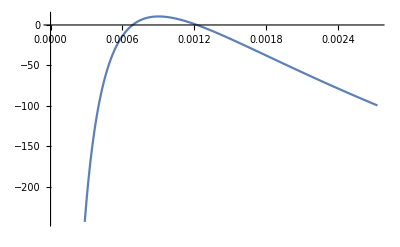
```mathematica
target=SimplifyLog[Log[Assuming[σSq>0&&λ>0&&n>0&&a≥0,(-D[f[t],t]/.t->0)PDF[NormalDistribution[μ0,√(σSq/n0)],a] -Graphics-PDF[InverseGammaDistribution[ν0/2,ν0σ0Sq/2],σSq] Pλ[n,a]//Simplify]]]
```

```mathematica
-(a^2 n0-2 a n0 μ0+n0 μ0^2+ν0σ0Sq+2 λ σSq)/(2 σSq)+(-1/2-ν0/2) Log[2]-Log[π]/2+(-a+n) Log[λ]+1/2 (Log[n0]-Log[σSq])+1/2 ν0 (Log[ν0σ0Sq]-Log[σS-Graphics-q])-Log[σSq]+Log[(ⅇ^(-(λ μ^2)/(2 σSq)) √λ √σSq)/(√(2 π))+1/2 λ μ (1+Erf[(√λ μ)/(√2 √σSq)])]-Log[Gamma[1-a+n]]-Log[Gamma[ν0/2]]
```

Analytical expressions not found in reasonable time

```mathematica
(*Integrate[Pλ[n,a] (-D[f[t],t]/.t->0),{λ,0,∞}]*)
```

```mathematica
Grad[target,{λ,μ,σSq}]//Simplify//TraditionalForm
```

{(n-a)/λ+(1/2 μ (erf((√λ μ)/(√2 √σSq))+1)+(√σSq ⅇ^(-(λ μ^2)/(2 σSq)))/(2 √(2 π) √λ))/(1/2 λ μ (erf((√λ μ)/(√2 √σSq))+1)+(√λ √σSq ⅇ^(-(λ μ^2)/(2 σSq)))/(√(2 π)))-1,(λ (erf((√λ μ)/(√2 √σSq))+1))/(2 (1/2 λ μ (erf((√λ μ)/(√2 √σSq))+1)+(√λ √σSq ⅇ^(-(λ μ^2)/(2 σSq)))/(√(2 π)))),(a^2 n0-2 a μ0 n0+(√2 σSq^(3/2))/(√π √λ μ ⅇ^((λ μ^2)/(2 σSq)) erf((√λ μ)/(√2 √σSq))+√π √λ μ ⅇ^((λ μ^2)/(2 σSq))+√2 √σSq)-ν0 σSq+ν0σ0Sq+μ0^2 n0-3 σSq)/(2 σSq^2)}

```mathematica
(-D[target,{{λ,μ,σSq},2}])//Simplify//TraditionalForm
```

```mathematica
({{((1/2 μ (erf((√λ μ)/(√2 √σSq))+1)+(ⅇ^(-(λ μ^2)/(2 σSq)) √σSq)/(2 √(2 π) √λ))^2)/((1/2 λ μ (erf((√λ μ)/(√2 √σSq))+1)+(ⅇ^(-(λ μ^2)/(2 σSq)) √λ √σSq)/(√(2 π)))^2)+(σSq-λ μ^2)/(2 λ^2 √σSq (ⅇ^((λ μ^2)/(2 σSq)) √(2 π) √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √(2 π) √λ μ+2 √σSq))+(n-a)/λ^2, (-2 √λ √σSq μ-ⅇ^((λ μ^2)/(2 σSq)) √(2 π) (λ μ^2+σSq)-ⅇ^((λ μ^2)/(2 σSq)) √(2 π) (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq)))/(2 √λ √σSq (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2), (μ (√2 √λ √σSq μ+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq)+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq))))/(2 √2 √λ σSq^(3/2) (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2)}, {(-2 √λ √σSq μ-ⅇ^((λ μ^2)/(2 σSq)) √(2 π) (λ μ^2+σSq)-ⅇ^((λ μ^2)/(2 σSq)) √(2 π) (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq)))/(2 √λ √σSq (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq3)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2), 1/4 λ ((λ (erf((√λ μ)/(√2 √σSq))+1)^2)/((1/2 λ μ (erf((√λ μ)/(√2 √σSq))+1)+(ⅇ^(-(λ μ^2)/(2 σSq)) √λ √σSq)/(√(2 π)))^2)-(4 √2)/(√σSq (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq))), (√λ (√2 √λ √σSq μ+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq)+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq))))/(√2 σSq^(3/2) (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2)}, {(μ (√2 √λ √σSq μ+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq)+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq))))/(2 √2 √λ σSq^(3/2) (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2), (√λ (√2 √λ √σSq μ+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq)+ⅇ^((λ μ^2)/(2 σSq)) √π (λ μ^2+σSq) erf((√λ μ)/(√2 √σSq))))/(√2 σSq^(3/2) (ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)^2), (8 n0 a^2-16 n0 μ0 a+8 n0 μ0^2+8 ν0σ0Sq-4 ν0 σSq-12 σSq+(2 √2 σSq^(3/2))/(ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)-(2 √2 λ μ^2 √σSq)/(ⅇ^((λ μ^2)/(2 σSq)) √π √λ erf((√λ μ)/(√2 √σSq)) μ+ⅇ^((λ μ^2)/(2 σSq)) √π √λ μ+√2 √σSq)+(ⅇ^(-(λ μ^2)/σSq) λ σSq^2)/(π (1/2 λ μ (erf((√λ μ)/(√2 √σSq))+1)+(ⅇ^(-(λ μ^2)/(2 σSq)) √λ √σSq)/(√(2 π)))^2))/(8 σSq^3)}})
```

```mathematica
Variance[{1,2}]
```

1/2